# Collision II

## Lab Report

Names: Aryan Malhotra
Section: H6
Date: 10/22/2024

## Purpose

To investigate the conservation of momentum and the conservation of energy in elastic and inelastic collisions.

## Readings

Explore these concepts either using Wikipedia or your favorite mechanics textbook,
Conservation of Energy,  Conservation of momentum,  Elastic collision, Inelastic collision, Kinematics, kinematics equations, Conservative forces

### Theory and concepts in short

Last week we looked at the relationship between change in momentum and impulse. In this week’s lab we will investigate conservation of momentum in collisions, and investigate the behavior of kinetic energy in collisions.

In the absence of external forces, or considering that the collision time is small enough for the ∫ F_ext dt to be negligible, the total momentum of a system is conserved. In the two body collision the total momentum of the system before and after the collision are given by,

-Graphics-
where the subscripts “i” and “f” stand for “initial” and “final.”

Mechanical energy is the sum of kinetic and potential energies. The law of conservation of energy states that the total energy of a system is always conserved. However, unlike momentum and total energy, kinetic energy is not usually conserved. The total kinetic energy of a two body system before and after a collision are given by,
-Graphics-

Notice that this is a scalar quantity. A collision in which kinetic energy is conserved is an elastic collision. In an inelastic collision some of the kinetic energy is converted into non-mechanical energy (often heat). Total energy is still conserved, but mechanical energy is not. Inelastic collisions in which two bodies stick together (sometimes called perfectly inelastic collisions) have the maximum loss of kinetic energy.

In the collisions we will consider in today’s lab there will be no change in potential energy (if the track is properly leveled), so we will ignore it.

## Procedure

In this experiment we will explore momentum, mechanical energy conservation (or non-conservation) in several types of collisions. You will determine the velocities of two “low-friction” carts with ultrasonic position rangers located on both ends of the 2 meter long aluminum track. The mass of a cart is 500 g (which you should check with a scale). Each cart might hold one or two additional 500 g weights. 
One end of each cart have Velcro pads attached to it so that if the carts touch by those ends, they will stick together. There are repelling magnets at the other ends of carts to allow for collisions that are more nearly elastic.

WARNINGS
- Do not slam or drop the carts or motion sensors.
- The carts are magnetic so do not bring them near anything using magnetic data storage, such as the computer or your credit cards.
- Catch the carts before they hit the motion sensors.

### Setting Up the Data Collection Program LoggerPro

You will determine the velocities of several “low-friction” carts with ultrasonic position rangers located on both ends of the 2 meter long aluminum track.
- Add the motion detector by clicking on the Vernier icon, ,
  and then clicking on DIG/SONIC1 ⇒ Choose Sensor ⇒ Motion Detector

{-Graphics-}
- Add the second Motion detector to  DIG/SONIC2.
- Click on the clock icon  and set the frequency to 50 Hz.
- Verify that the track is level. If the track is not level you will notice that a cart, when given a gentle push in one direction will stop and reverse direction. If pushed in the opposite direction it may gain speed, although this may not be noticeable due to friction.

- The motion sensors are working with sonar. They send sound pulses and listen to the echo. This is why you need to be careful when setting two sonars which work similarly in front of each other. They might listen to each other instead of the echo coming from the object we want to measure the position of. If you can not get a ‘good’ data, i.e. without any jumps caused by other motion sensor’s pulses, try to change their angles a little (~2~3°) towards the track. Also be sure to use the NARROW settings of the motion detectors.

- Calibrating the positive direction: Define common displacement direction, i.e. the positive direction for the position axis. You need to check Reverse Direction for one of the motion detectors depending which direction you choose as positive.
- Calibrating the position origin: To make the position graphs look more intuitive, try to make the position origin, x=0, to be the same on the graphs. To do this attach both carts in the middle of the track using their Velcro sides and make them stand still. Now Zero both the detectors.

## Dialog:

The lab entails investigating these four different types of collisions:
1. Elastic collision (magnet):      m1 = m2,  v1 > 0,  v2 = 0
2. Inelastic collision (Velcro):     m1 = m2,  v1 > 0,  v2 = 0
3. Elastic collision (magnet):      m1 = m2,  v1 > 0,  v2 ≠ 0        (one fast, one slow!)
4. Elastic collision (magnet):      m1 < m2,  v1 > 0,  v2 = 0

- Set up the LoggerPro and be sure to record positions the cart from times far enough from the collision.
Try to have smooth data for at least one second before the collision and one second after the collision.
- Define Zero and the positive direction. See the calibrating paragraphs in the Procedure section.
- For each step, record and save the positions of both cart. Export your data in CVS format and Import it into Mathematica using the Import command. 
- For each step, calculate the velocity of each cart before and after the collision from the slop of position vs time plot as you did in the prerequisite assignment.
Here is an example which shows one way to calculate the velocities:

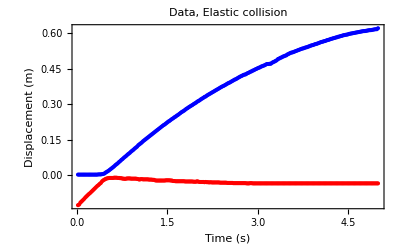

```mathematica
expax1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiona2.csv"],     All, {1, 2}]];   (*Position vs time for cart 1*)
expax2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiona2.csv"],     All, {1, 5}]];  (*Position vs time for cart 2*)
expavel1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiona2.csv"],     All, {1, 3}]];   (*Velocity vs time for cart 1*)
expavel2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiona2.csv"],     All, {1, 6}]];  (*Velocity vs time for cart 2*)
Show[ListPlot[expax1,PlotStyle->Red],ListPlot[expax2,PlotStyle->Blue], PlotRange-> All,  PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]
```

From the Plot, find t0, t1 and t2, and update them below:

```mathematica
expat0 = 0;     (* time of start, for the fit *)
expat1 = 0.46;     (* the time of collision: rightclick on the position vs time plot, and choose "Get Coordinate" to find the time of collision t1 *)
expat2=1;      (* time of end, for the fit *)
```

```mathematica
(* The code below first fits quadratic curves on the position data of each cart before and after the collision. Total of four quadratic curves (line11, line12, line21, and line22). Then measures the velocities of each cart right before and right after the collision by taking the derivatives of these smooth curves at t1. Measuring t1 as acurate as possible is crucial. *)
expaline11 = Fit[Select[expax1, expat0 < First[#] < expat1 - .05 &], {1, t, t^2}, t]; (* fit to a quadratic function of t  *)
expaline12 = Fit[Select[expax1, expat1 + .05 < First[#] < expat2 &], {1, t, t^2}, t];
expaline21 = Fit[Select[expax2, expat0 < First[#] < expat1 - .05 &], {1, t, t^2}, t];
expaline22 = Fit[Select[expax2, expat1 + .05 < First[#] < expat2 &], {1, t, t^2}, t];
expav1i = D[expaline11, t] /. t -> expat1;
expav1f = D[expaline12, t] /. t -> expat1;
expav2i = D[expaline21, t] /. t -> expat1;
expav2f = D[expaline22, t] /. t -> expat1;
```

0.46 collision time |  |  | 
expav1i, m/s | expav1f, m/s | expav2i, m/s | expav2f, m/s
0.217 | -0.00722 | 0.0104 | 0.211

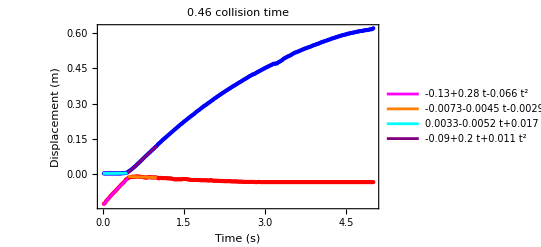

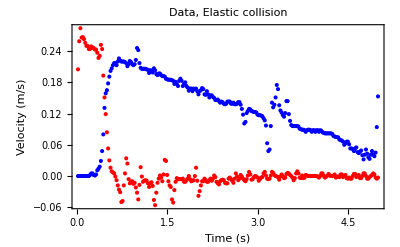

```mathematica
Grid[{{Text["collision time" expat1], SpanFromLeft}, {"expav1i, m/s","expav1f, m/s", "expav2i, m/s","expav2f, m/s"},{NumberForm[expav1i, 3], NumberForm[expav1f, 3], NumberForm[expav2i, 3], NumberForm[expav2f, 3]}}, Frame -> All]
Show[ListPlot[expax1, PlotStyle -> Red], Plot[expaline11, {t, 0, expat1}, PlotStyle -> Magenta, PlotLegends -> {NumberForm[expaline11, 2], ""}],Plot[expaline12, {t, expat1, expat2}, PlotStyle -> Orange, 
  PlotLegends -> { NumberForm[expaline12, 2], ""}], 
ListPlot[expax2, PlotStyle -> Blue], Plot[expaline21, {t, 0, expat1}, PlotStyle -> Cyan, PlotLegends -> {NumberForm[expaline21, 2], ""}],Plot[expaline22, {t, expat1, expat2}, PlotStyle -> Purple, 
  PlotLegends -> { NumberForm[expaline22, 2], ""}],  PlotRange-> All, PlotLabel -> "collision time" expat1 , Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]
Show[ListPlot[expavel1,PlotStyle->Red],ListPlot[expavel2,PlotStyle->Blue],  PlotRange-> All, PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Velocity (m/s)"}]
```

### Step 1. Elastic collision (magnet): m1 = m2, v1 > 0, v2 = 0

- Measure the mass of each cart using the scale.
- Set the carts on the track with their magnetic sides facing each other.
- Record the position of the carts during the collision.
- Calculate the velocity of each cart before and after collisions as explained above. 
- Calculate the initial and final momentum and kinetic energy.
- Plot the data, fit the data to determine velocities before and after collision.
- Present your findings in the table below.

```mathematica
expam1=  .4830       (* mass of the first cart in experiment a -> cart on the left*) 
expam2=  .4795       (* mass of the second cart in experiment a -> cart on the right*)

Grid[{{Text["m1 = m2,  v1 > 0,  v2 = 0"],SpanFromLeft},{"Type of Collision","m1, kg","v1i, m/s","v1f, m/s","m2, kg","v2i, m/s","v2f, m/s","Pi, kg.m/s","Pf, kg.m/s","KEi, J", "KEf, J","Pf/Pi","KEf/KEi"}, {"Elastic",expam1,NumberForm[expav1i,2],NumberForm[expav1f,2],expam2,NumberForm[expav2i,2], NumberForm[expav2f,2],NumberForm[expam1*expav1i+expam2*expav2i,2],NumberForm[expam1*expav1f+expam2*expav2f,2],NumberForm[1/2*expam1*expav1i^2+1/2*expam2*expav2i^2,2],NumberForm[1/2*expam1*expav1f^2+1/2*expam2*expav2f^2,2],NumberForm[(expam1*expav1f+expam2*expav2f)/(expam1*expav1i+expam2*expav2i),2],NumberForm[(1/2*expam1*expav1f^2+1/2*expam2*expav2f^2)/(1/2*expam1*expav1i^2+1/2*expam2*expav2i^2),2]}}, Frame -> All]
```

0.483

0.4795

m1 = m2,  v1 > 0,  v2 = 0 |  |  |  |  |  |  |  |  |  |  |  | 
Type of Collision | m1, kg | v1i, m/s | v1f, m/s | m2, kg | v2i, m/s | v2f, m/s | Pi, kg.m/s | Pf, kg.m/s | KEi, J | KEf, J | Pf/Pi | KEf/KEi
Elastic | 0.483 | 0.22 | -0.0072 | 0.4795 | 0.01 | 0.21 | 0.11 | 0.098 | 0.011 | 0.011 | 0.89 | 0.94

### Step 2. Inelastic collision (Velcro): m1 = m2, v1 > 0, v2 = 0

- Set the carts on the track with their Velcro sides facing each other.
- Calculate the initial and final momentum and kinetic energy.
- Plot the data, fit the data to determine velocities before and after collision.
- Present your findings in the table below.

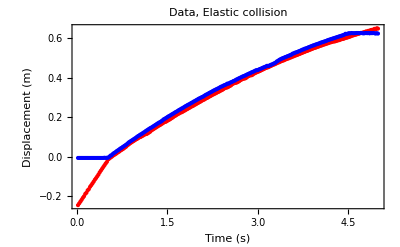

0.52 collision time |  |  | 
expbv1i, m/s | expbv1f, m/s | expbv2i, m/s | expbv2f, m/s
0.46 | 0.207 | 0.00359 | 0.223

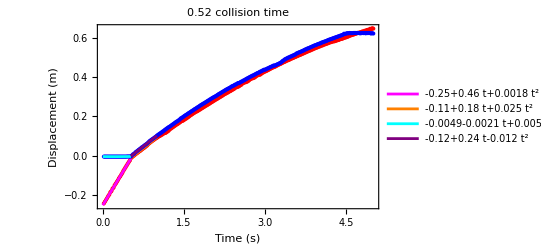

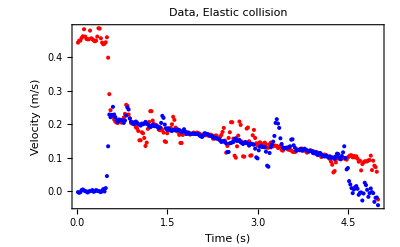

m1 = m2,  v1 > 0,  v2 = 0 |  |  |  |  |  |  |  |  |  |  |  | 
Type of Collision | m1, kg | v1i, m/s | v1f, m/s | m2, kg | v2i, m/s | v2f, m/s | Pi, kg.m/s | Pf, kg.m/s | KEi, J | KEf, J | Pf/Pi | KEf/KEi
InElastic | 0.483 | 0.46 | 0.21 | 0.4795 | 0.0036 | 0.22 | 0.22 | 0.21 | 0.051 | 0.022 | 0.92 | 0.44

```mathematica
expbx1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionb2.csv"],     All, {1, 2}]];   (*Position vs time for cart 1*)
expbx2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionb2.csv"],     All, {1, 5}]];  (*Position vs time for cart 2*)
expbvel1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionb2.csv"],     All, {1, 3}]];   (*Velocity vs time for cart 1*)
expbvel2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionb2.csv"],     All, {1, 6}]];  (*Velocity vs time for cart 2*)
Show[ListPlot[expbx1,PlotStyle->Red],ListPlot[expbx2,PlotStyle->Blue], PlotRange-> All,  PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]

expbt0 = 0;     (* time of start, for the fit *)
expbt1 = 0.52;     (* the time of collision: rightclick on the position vs time plot, and choose "Get Coordinate" to find the time of collision t1 *)
expbt2=1;      (* time of end, for the fit *)

expbline11 = Fit[Select[expbx1, expbt0 < First[#] < expbt1 - .05 &], {1, t, t^2}, t]; (* fit to a quadratic function of t  *)
expbline12 = Fit[Select[expbx1, expbt1 + .05 < First[#] < expbt2 &], {1, t, t^2}, t];
expbline21 = Fit[Select[expbx2, expbt0 < First[#] < expbt1 - .05 &], {1, t, t^2}, t];
expbline22 = Fit[Select[expbx2, expbt1 + .05 < First[#] < expbt2 &], {1, t, t^2}, t];
expbv1i = D[expbline11, t] /. t -> expbt1;
expbv1f = D[expbline12, t] /. t -> expbt1;
expbv2i = D[expbline21, t] /. t -> expbt1;
expbv2f = D[expbline22, t] /. t -> expbt1;

expbm1=  .4830 ;      (* mass of the first cart in experiment a -> cart on the left*) 
expbm2=  .4795   ;    (* mass of the second cart in experiment a -> cart on the right*)


Grid[{{Text["collision time" expbt1], SpanFromLeft}, {"expbv1i, m/s","expbv1f, m/s", "expbv2i, m/s","expbv2f, m/s"},{NumberForm[expbv1i, 3], NumberForm[expbv1f, 3], NumberForm[expbv2i, 3], NumberForm[expbv2f, 3]}}, Frame -> All]
Show[ListPlot[expbx1, PlotStyle -> Red], Plot[expbline11, {t, 0, expbt1}, PlotStyle -> Magenta, PlotLegends -> {NumberForm[expbline11, 2], ""}],Plot[expbline12, {t, expbt1, expbt2}, PlotStyle -> Orange, 
  PlotLegends -> { NumberForm[expbline12, 2], ""}], 
ListPlot[expbx2, PlotStyle -> Blue], Plot[expbline21, {t, 0, expbt1}, PlotStyle -> Cyan, PlotLegends -> {NumberForm[expbline21, 2], ""}],Plot[expbline22, {t, expbt1, expbt2}, PlotStyle -> Purple, 
  PlotLegends -> { NumberForm[expbline22, 2], ""}],  PlotRange-> All, PlotLabel -> "collision time" expbt1 , Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]
Show[ListPlot[expbvel1,PlotStyle->Red],ListPlot[expbvel2,PlotStyle->Blue],  PlotRange-> All, PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Velocity (m/s)"}]

Grid[{{Text["m1 = m2,  v1 > 0,  v2 = 0"],SpanFromLeft},{"Type of Collision","m1, kg","v1i, m/s","v1f, m/s","m2, kg","v2i, m/s","v2f, m/s","Pi, kg.m/s","Pf, kg.m/s","KEi, J", "KEf, J","Pf/Pi","KEf/KEi"}, {"InElastic",expbm1,NumberForm[expbv1i,2],NumberForm[expbv1f,2],expbm2,NumberForm[expbv2i,2], NumberForm[expbv2f,2],NumberForm[expbm1*expbv1i+expbm2*expbv2i,2],NumberForm[expbm1*expbv1f+expbm2*expbv2f,2],NumberForm[1/2*expbm1*expbv1i^2+1/2*expbm2*expbv2i^2,2],NumberForm[1/2*expbm1*expbv1f^2+1/2*expbm2*expbv2f^2,2],NumberForm[(expbm1*expbv1f+expbm2*expbv2f)/(expbm1*expbv1i+expbm2*expbv2i),2],NumberForm[(1/2*expbm1*expbv1f^2+1/2*expbm2*expbv2f^2)/(1/2*expbm1*expbv1i^2+1/2*expbm2*expbv2i^2),2]}}, Frame -> All]
```

### Step 3. Elastic collision (magnet): m1 = m2, v1 > 0, v2 ≠ 0 (one fast, one slow!)

- Repeat the elastic collisions with now both carts in motion before the collision.
- Calculate the initial and final momentum and kinetic energy.
- Plot the data, fit the data to determine velocities before and after collision.
- Present your findings in the table below.

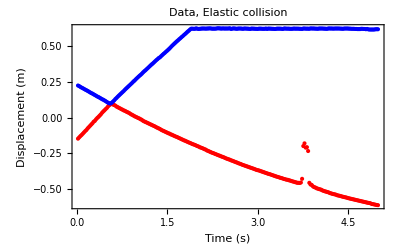

0.55 collision time |  |  | 
expcv1i, m/s | expcv1f, m/s | expcv2i, m/s | expcv2f, m/s
0.462 | -0.226 | -0.238 | 0.423

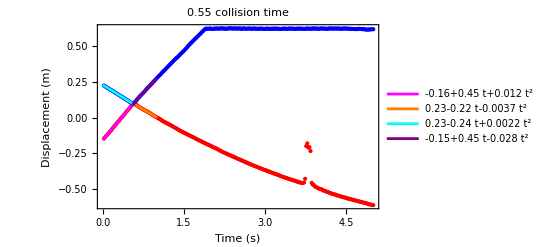

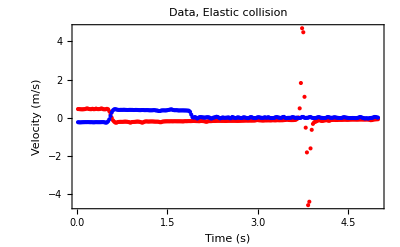

m1 = m2,  v1 > 0,  v2 = 0 |  |  |  |  |  |  |  |  |  |  |  | 
Type of Collision | m1, kg | v1i, m/s | v1f, m/s | m2, kg | v2i, m/s | v2f, m/s | Pi, kg.m/s | Pf, kg.m/s | KEi, J | KEf, J | Pf/Pi | KEf/KEi
Elastic | 0.483 | 0.46 | -0.23 | 0.4795 | -0.24 | 0.42 | 0.11 | 0.094 | 0.065 | 0.055 | 0.86 | 0.85

```mathematica
expcx1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionc3.csv"],     All, {1, 2}]];   (*Position vs time for cart 1*)
expcx2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionc3.csv"],     All, {1, 5}]];  (*Position vs time for cart 2*)
expcvel1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionc3.csv"],     All, {1, 3}]];   (*Velocity vs time for cart 1*)
expcvel2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisionc3.csv"],     All, {1, 6}]];  (*Velocity vs time for cart 2*)
Show[ListPlot[expcx1,PlotStyle->Red],ListPlot[expcx2,PlotStyle->Blue], PlotRange-> All,  PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]

expct0 = 0;     (* time of start, for the fit *)
expct1 = 0.55;     (* the time of collision: rightclick on the position vs time plot, and choose "Get Coordinate" to find the time of collision t1 *)
expct2=1;      (* time of end, for the fit *)

expcline11 = Fit[Select[expcx1, expct0 < First[#] < expct1 - .05 &], {1, t, t^2}, t]; (* fit to a quadratic function of t  *)
expcline12 = Fit[Select[expcx1, expct1 + .05 < First[#] < expct2 &], {1, t, t^2}, t];
expcline21 = Fit[Select[expcx2, expct0 < First[#] < expct1 - .05 &], {1, t, t^2}, t];
expcline22 = Fit[Select[expcx2, expct1 + .05 < First[#] < expct2 &], {1, t, t^2}, t];
expcv1i = D[expcline11, t] /. t -> expct1;
expcv1f = D[expcline12, t] /. t -> expct1;
expcv2i = D[expcline21, t] /. t -> expct1;
expcv2f = D[expcline22, t] /. t -> expct1;

expcm1=  .4830 ;      (* mass of the first cart in experiment a -> cart on the left*) 
expcm2=  .4795   ;    (* mass of the second cart in experiment a -> cart on the right*)


Grid[{{Text["collision time" expct1], SpanFromLeft}, {"expcv1i, m/s","expcv1f, m/s", "expcv2i, m/s","expcv2f, m/s"},{NumberForm[expcv1i, 3], NumberForm[expcv1f, 3], NumberForm[expcv2i, 3], NumberForm[expcv2f, 3]}}, Frame -> All]
Show[ListPlot[expcx1, PlotStyle -> Red], Plot[expcline11, {t, 0, expct1}, PlotStyle -> Magenta, PlotLegends -> {NumberForm[expcline11, 2], ""}],Plot[expcline12, {t, expct1, expct2}, PlotStyle -> Orange, 
  PlotLegends -> { NumberForm[expcline12, 2], ""}], 
ListPlot[expcx2, PlotStyle -> Blue], Plot[expcline21, {t, 0, expct1}, PlotStyle -> Cyan, PlotLegends -> {NumberForm[expcline21, 2], ""}],Plot[expcline22, {t, expct1, expct2}, PlotStyle -> Purple, 
  PlotLegends -> { NumberForm[expcline22, 2], ""}],  PlotRange-> All, PlotLabel -> "collision time" expct1 , Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]
Show[ListPlot[expcvel1,PlotStyle->Red],ListPlot[expcvel2,PlotStyle->Blue],  PlotRange-> All, PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Velocity (m/s)"}]

Grid[{{Text["m1 = m2,  v1 > 0,  v2 = 0"],SpanFromLeft},{"Type of Collision","m1, kg","v1i, m/s","v1f, m/s","m2, kg","v2i, m/s","v2f, m/s","Pi, kg.m/s","Pf, kg.m/s","KEi, J", "KEf, J","Pf/Pi","KEf/KEi"}, {"Elastic",expcm1,NumberForm[expcv1i,2],NumberForm[expcv1f,2],expcm2,NumberForm[expcv2i,2], NumberForm[expcv2f,2],NumberForm[expcm1*expcv1i+expcm2*expcv2i,2],NumberForm[expcm1*expcv1f+expcm2*expcv2f,2],NumberForm[1/2*expcm1*expcv1i^2+1/2*expcm2*expcv2i^2,2],NumberForm[1/2*expcm1*expcv1f^2+1/2*expcm2*expcv2f^2,2],NumberForm[(expcm1*expcv1f+expcm2*expcv2f)/(expcm1*expcv1i+expcm2*expcv2i),2],NumberForm[(1/2*expcm1*expcv1f^2+1/2*expcm2*expcv2f^2)/(1/2*expcm1*expcv1i^2+1/2*expcm2*expcv2i^2),2]}}, Frame -> All]
```

### Step 4. Elastic collision (magnet): m1 < m2, v1 > 0, v2 = 0

- Put one or two additional weights on one of the carts and repeat the elastic collisions.
- Calculate the initial and final momentum and kinetic energy.
- Plot the data, fit the data to determine velocities before and after collision.
- Present your findings in the table below.

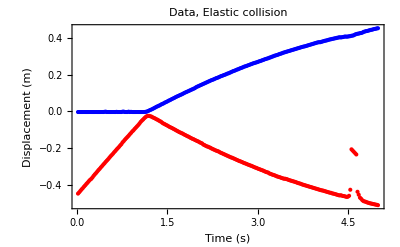

1.18 collision time |  |  | 
expdv1i, m/s | expdv1f, m/s | expdv2i, m/s | expdv2f, m/s
0.371 | -0.197 | -0.00143 | 0.173

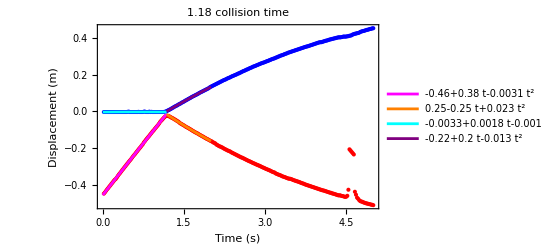

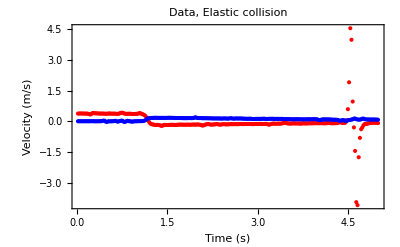

m1 = m2,  v1 > 0,  v2 = 0 |  |  |  |  |  |  |  |  |  |  |  | 
Type of Collision | m1, kg | v1i, m/s | v1f, m/s | m2, kg | v2i, m/s | v2f, m/s | Pi, kg.m/s | Pf, kg.m/s | KEi, J | KEf, J | Pf/Pi | KEf/KEi
Elastic | 0.483 | 0.37 | -0.2 | 1.467 | -0.0014 | 0.17 | 0.18 | 0.16 | 0.033 | 0.031 | 0.89 | 0.94

```mathematica
expdx1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiond1.csv"],     All, {1, 2}]];   (*Position vs time for cart 1*)
expdx2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiond1.csv"],     All, {1, 5}]];  (*Position vs time for cart 2*)
expdvel1 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiond1.csv"],     All, {1, 3}]];   (*Velocity vs time for cart 1*)
expdvel2 = Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 6\\collisiond1.csv"],     All, {1, 6}]];  (*Velocity vs time for cart 2*)
Show[ListPlot[expdx1,PlotStyle->Red],ListPlot[expdx2,PlotStyle->Blue], PlotRange-> All,  PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]

expdt0 = 0;     (* time of start, for the fit *)
expdt1 = 1.18;     (* the time of collision: rightclick on the position vs time plot, and choose "Get Coordinate" to find the time of collision t1 *)
expdt2=2;      (* time of end, for the fit *)

expdline11 = Fit[Select[expdx1, expdt0 < First[#] < expdt1 - .05 &], {1, t, t^2}, t]; (* fit to a quadratic function of t  *)
expdline12 = Fit[Select[expdx1, expdt1 + .05 < First[#] < expdt2 &], {1, t, t^2}, t];
expdline21 = Fit[Select[expdx2, expdt0 < First[#] < expdt1 - .05 &], {1, t, t^2}, t];
expdline22 = Fit[Select[expdx2, expdt1 + .05 < First[#] < expdt2 &], {1, t, t^2}, t];
expdv1i = D[expdline11, t] /. t -> expdt1;
expdv1f = D[expdline12, t] /. t -> expdt1;
expdv2i = D[expdline21, t] /. t -> expdt1;
expdv2f = D[expdline22, t] /. t -> expdt1;

expdm1=  .4830 ;      (* mass of the first cart in experiment a -> cart on the left*) 
expdm2=  1.467   ;    (* mass of the second cart in experiment a -> cart on the right*)


Grid[{{Text["collision time" expdt1], SpanFromLeft}, {"expdv1i, m/s","expdv1f, m/s", "expdv2i, m/s","expdv2f, m/s"},{NumberForm[expdv1i, 3], NumberForm[expdv1f, 3], NumberForm[expdv2i, 3], NumberForm[expdv2f, 3]}}, Frame -> All]
Show[ListPlot[expdx1, PlotStyle -> Red], Plot[expdline11, {t, 0, expdt1}, PlotStyle -> Magenta, PlotLegends -> {NumberForm[expdline11, 2], ""}],Plot[expdline12, {t, expdt1, expdt2}, PlotStyle -> Orange, 
  PlotLegends -> { NumberForm[expdline12, 2], ""}], 
ListPlot[expdx2, PlotStyle -> Blue], Plot[expdline21, {t, 0, expdt1}, PlotStyle -> Cyan, PlotLegends -> {NumberForm[expdline21, 2], ""}],Plot[expdline22, {t, expdt1, expdt2}, PlotStyle -> Purple, 
  PlotLegends -> { NumberForm[expdline22, 2], ""}],  PlotRange-> All, PlotLabel -> "collision time" expdt1 , Frame -> True,  FrameLabel -> {"Time (s)", "Displacement (m)"}]
Show[ListPlot[expdvel1,PlotStyle->Red],ListPlot[expdvel2,PlotStyle->Blue],  PlotRange-> All, PlotLabel -> "Data, Elastic collision", Frame -> True,  FrameLabel -> {"Time (s)", "Velocity (m/s)"}]

Grid[{{Text["m1 = m2,  v1 > 0,  v2 = 0"],SpanFromLeft},{"Type of Collision","m1, kg","v1i, m/s","v1f, m/s","m2, kg","v2i, m/s","v2f, m/s","Pi, kg.m/s","Pf, kg.m/s","KEi, J", "KEf, J","Pf/Pi","KEf/KEi"}, {"Elastic",expdm1,NumberForm[expdv1i,2],NumberForm[expdv1f,2],expdm2,NumberForm[expdv2i,2], NumberForm[expdv2f,2],NumberForm[expdm1*expdv1i+expdm2*expdv2i,2],NumberForm[expdm1*expdv1f+expdm2*expdv2f,2],NumberForm[1/2*expdm1*expdv1i^2+1/2*expdm2*expdv2i^2,2],NumberForm[1/2*expdm1*expdv1f^2+1/2*expdm2*expdv2f^2,2],NumberForm[(expdm1*expdv1f+expdm2*expdv2f)/(expdm1*expdv1i+expdm2*expdv2i),2],NumberForm[(1/2*expdm1*expdv1f^2+1/2*expdm2*expdv2f^2)/(1/2*expdm1*expdv1i^2+1/2*expdm2*expdv2i^2),2]}}, Frame -> All]
```

### Step 5.

- Present all your four findings in the combined table below and answer the following questions.

```mathematica
Grid[{{Text["Low friction cart collisions"],SpanFromLeft},{"Type of Collision","m1, kg","v1i, m/s","v1f, m/s","m2, kg","v2i, m/s","v2f, m/s","Pi, kg.m/s","Pf, kg.m/s","KEi, J", "KEf, J","Pf/Pi","KEf/KEi"}, {"Elastic",expam1,NumberForm[expav1i,2],NumberForm[expav1f,2],expam2,NumberForm[expav2i,2], NumberForm[expav2f,2],NumberForm[expam1*expav1i+expam2*expav2i,2],NumberForm[expam1*expav1f+expam2*expav2f,2],NumberForm[1/2*expam1*expav1i^2+1/2*expam2*expav2i^2,2],NumberForm[1/2*expam1*expav1f^2+1/2*expam2*expav2f^2,2],NumberForm[(expam1*expav1f+expam2*expav2f)/(expam1*expav1i+expam2*expav2i),2],NumberForm[(1/2*expam1*expav1f^2+1/2*expam2*expav2f^2)/(1/2*expam1*expav1i^2+1/2*expam2*expav2i^2),2]}, {"InElastic",expbm1,NumberForm[expbv1i,2],NumberForm[expbv1f,2],expbm2,NumberForm[expbv2i,2], NumberForm[expbv2f,2],NumberForm[expbm1*expbv1i+expbm2*expbv2i,2],NumberForm[expbm1*expbv1f+expbm2*expbv2f,2],NumberForm[1/2*expbm1*expbv1i^2+1/2*expbm2*expbv2i^2,2],NumberForm[1/2*expbm1*expbv1f^2+1/2*expbm2*expbv2f^2,2],NumberForm[(expbm1*expbv1f+expbm2*expbv2f)/(expbm1*expbv1i+expbm2*expbv2i),2],NumberForm[(1/2*expbm1*expbv1f^2+1/2*expbm2*expbv2f^2)/(1/2*expbm1*expbv1i^2+1/2*expbm2*expbv2i^2),2]}, {"Elastic",expcm1,NumberForm[expcv1i,2],NumberForm[expcv1f,2],expcm2,NumberForm[expcv2i,2], NumberForm[expcv2f,2],NumberForm[expcm1*expcv1i+expcm2*expcv2i,2],NumberForm[expcm1*expcv1f+expcm2*expcv2f,2],NumberForm[1/2*expcm1*expcv1i^2+1/2*expcm2*expcv2i^2,2],NumberForm[1/2*expcm1*expcv1f^2+1/2*expcm2*expcv2f^2,2],NumberForm[(expcm1*expcv1f+expcm2*expcv2f)/(expcm1*expcv1i+expcm2*expcv2i),2],NumberForm[(1/2*expcm1*expcv1f^2+1/2*expcm2*expcv2f^2)/(1/2*expcm1*expcv1i^2+1/2*expcm2*expcv2i^2),2]},{"Elastic",expdm1,NumberForm[expdv1i,2],NumberForm[expdv1f,2],expdm2,NumberForm[expdv2i,2], NumberForm[expdv2f,2],NumberForm[expdm1*expdv1i+expdm2*expdv2i,2],NumberForm[expdm1*expdv1f+expdm2*expdv2f,2],NumberForm[1/2*expdm1*expdv1i^2+1/2*expdm2*expdv2i^2,2],NumberForm[1/2*expdm1*expdv1f^2+1/2*expdm2*expdv2f^2,2],NumberForm[(expdm1*expdv1f+expdm2*expdv2f)/(expdm1*expdv1i+expdm2*expdv2i),2],NumberForm[(1/2*expdm1*expdv1f^2+1/2*expdm2*expdv2f^2)/(1/2*expdm1*expdv1i^2+1/2*expdm2*expdv2i^2),2]}}, Frame -> All]
```

Low friction cart collisions |  |  |  |  |  |  |  |  |  |  |  | 
Type of Collision | m1, kg | v1i, m/s | v1f, m/s | m2, kg | v2i, m/s | v2f, m/s | Pi, kg.m/s | Pf, kg.m/s | KEi, J | KEf, J | Pf/Pi | KEf/KEi
Elastic | 0.483 | 0.22 | -0.0072 | 0.4795 | 0.01 | 0.21 | 0.11 | 0.098 | 0.011 | 0.011 | 0.89 | 0.94
InElastic | 0.483 | 0.46 | 0.21 | 0.4795 | 0.0036 | 0.22 | 0.22 | 0.21 | 0.051 | 0.022 | 0.92 | 0.44
Elastic | 0.483 | 0.46 | -0.23 | 0.4795 | -0.24 | 0.42 | 0.11 | 0.094 | 0.065 | 0.055 | 0.86 | 0.85
Elastic | 0.483 | 0.37 | -0.2 | 1.467 | -0.0014 | 0.17 | 0.18 | 0.16 | 0.033 | 0.031 | 0.89 | 0.94

#### Question 1. - Is the conservation of energy violated in the inelastic collision? Explain. - For step 2, use only the initial velocity data, and also the conservation of momentum law, to estimate theoretical value for KEf/KEi. Is this close to the value KEf/KEi you have measured?

#### The data shows a value of KEf/KEi = 0.44 for an inelastic collision. This suggests that the final kinetic energy is 44% of the initial kinetic energy, indicating that 56% of the energy is lost, which is expected in an inelastic collision. Energy is not conserved in inelastic collisions because some of it is converted to other forms like heat or sound. Therefore, yes, the conservation of energy is violated, as the ratio suggests significant energy loss. Theoretically, the energy loss in an inelastic collision should be close to 50%, and when I looked at my results, I got around 0.44, which is quite close to that. So, even though some of the initial energy is lost, it’s within expected ranges for inelastic collisions.

#### Question 2. (Review) - What is the theoretical value for Pf/Pi for the steps 1, 2, 3, and 4? - What is the theoretical value for KEf/KEi for the steps 1, 2, 3, and 4? See the above question for step 2.

#### For momentum, it makes sense that it should stay the same since no external force should be acting on the system ideally. So, in all cases, the theoretical value for Pf/Pi should be 1, meaning the momentum before and after should be the same. In my results, it’s not always exactly 1, but that’s probably due to small external forces like friction. For KEf/KEi, in an elastic collision, energy should stay the same for elastic collisions and 0.5 for inelastic collisions, meaning the ratio should be 1. But in an inelastic collision, the energy is supposed to be less, and my value of 0.44 shows how much energy is lost, which again matches theory well.

#### Question 3. - Which collision was most nearly elastic? Why do you think so? - In which collision friction has a bigger effect? Why do you think so?

#### 1st and 3rd are the closest to being perfectly elastic since ke1/ke2 is closest to 1 for both. By definition, Kinetic energy is conserved in an elastic collision meaning ke1/ke2 must be 1.

#### Question 4. - How does friction affect Pf/Pi ratio? - By estimating F_ext of the friction and Δt for the collision time, try to see if your reasoning above is correct. In other words, try to falsify yourself.

#### Since friction is an unaccounted force in the same direction as the velocity of the carts, it would impact the momentum of the system. Friction takes energy away from the system and would hence mean our final momentum would be less than the initial momentum. For exp 4, F_(ext(avg)) = -3N an obvious thing would be to see what the coefficient of friction is. It should me = μmg = μ * 15 hence, μ must be about 0.2 (seems low enough)? To verify further, outside of collision, again for 4th experiment, x(1.5) = 0.054, x(3)=2.69, v(1.5)=0.166 del x = v0t + at^2/2 f = ma = m * (del x - v0t) * 2/t^2 = 0.3112 Which is almost the same magnitude as the estimated force!! So yes, my explanation seems incredibly nice!

```mathematica
delt = 0.02
Impulse = -0.06
F = Impulse/delt
N[3/15]
N[1.467*((2.69-0.054)-0.166*1.5)*2/1.5^2]
```

0.02

-0.06

-3.

0.2

3.11265

Rutgers 275 Classical Physics Lab
“Collisions-II”
Contributed by Maryam Taherinejad and Girsh Blumberg ©2014